```mathematica
CC
```

所有临时定义已清空!

```mathematica
ECplus[p1_,p2_]:=Block[
{a,b,k,x3,x1,y1,x2,y2},
{a,b}=para;{x1,y1}=p1;{x2,y2}=p2;
If[p1!=p2,k=(y1-y2)/(x1-x2),k=(3x1^2+a)/(2y1)];
{x3=k^2-x1-x2,-(y1+k(x3-x1))}
]
ECplusN[p1,p2]
ECplus[p1,p2]
```

```mathematica
x(x^2+109*x+224)/.x:>x-109/3//Expand//Together
```

1/27 (2370314-100881 x+27 x^3)

```mathematica
A=4n^2+12n-3;B=32(n+3);
y^2==x(x^2+A x+B)/.x:>x-A/3//Expand
```

y^2==94-328 n-344 n^2+(64 n^3)/3+(352 n^4)/3+(128 n^5)/3+(128 n^6)/27+93 x+56 n x-40 n^2 x-32 n^3 x-(16 n^4 x)/3+x^3

```mathematica
sol=Solve[{y^2==x(x^2+109*x+224),y>0,x!=0},{x,y},Integers];
DeleteCases[{x,y}/.sol,{x,ConditionalExpression[_,_]}]
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{-100,260},{-56,392},{-9,78},{-4,28}}

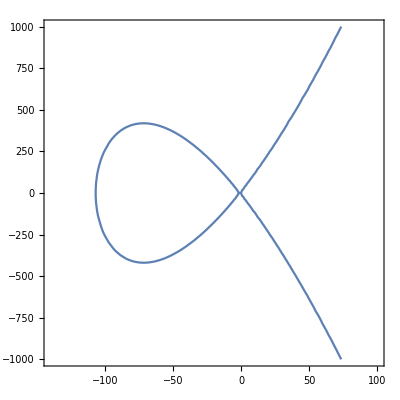

```mathematica
ContourPlot[y^2==x(x^2+109*x+224),{x,-140,100},{y,-1000,1000}]
```

```mathematica
ecr=ImplicitRegion[y^2==x (x-1) (x+1),{{x,-2,2},{y,-2,2}}];
BlockRandom[SeedRandom["elliptic"];(*for reproducibility*)(*Quiet suppresses a few harmless error messages*){p1,p2}=Quiet[RandomPoint[ecr,2]];]
```

```mathematica
n==a/(b+c)+b/(c+a)+c/(a+b)
```

n==c/(a+b)+b/(a+c)+a/(b+c)

```mathematica
CC
```

所有临时定义已清空!

```mathematica
Quit
```

```mathematica
DiophantineSolver[name_String,para_]:=Block[
{},
Switch[name,
"AndrewAllan",AndrewAllanSolver[para]


]
```

```mathematica
??ECplus
```

Information::notfound: 无法找到符号 ECplus.

```mathematica
AndrewAllan`Solver[4]
```

等价映射:  {AndrewAllan`x$7072==-(28 (AndrewAllan`a$7072+AndrewAllan`b$7072+2 AndrewAllan`c$7072))/(6 AndrewAllan`a$7072+5 AndrewAllan`b$7072-AndrewAllan`c$7072),AndrewAllan`y$7072==(364 (AndrewAllan`a$7072-AndrewAllan`b$7072))/(6 AndrewAllan`a$7072+5 AndrewAllan`b$7072-AndrewAllan`c$7072)}

等价椭圆曲线:  (AndrewAllan`y$7072)^2==AndrewAllan`x$7072 (224+109 AndrewAllan`x$7072+(AndrewAllan`x$7072)^2)

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{AndrewAllan`a$7072→154476802108746166441951315019919837485664325669565431700026634898253202035277999,AndrewAllan`b$7072→36875131794129999827197811565225474825492979968971970996283137471637224634055579,AndrewAllan`c$7072→4373612677928697257861252602371390152816537558161613618621437993378423467772036}

```mathematica
FindInstance[{y^2==x (352+349 x+x^2),x>0},{x,y},Integers]
```

{{x→4,y→-84}}